{-4.43486,0,5.72267×10^-8}

0.000239221

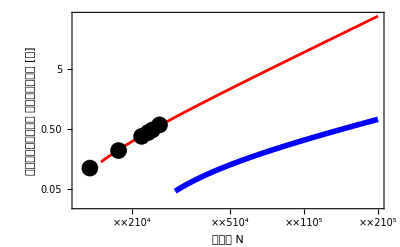

```mathematica
ClearAll["Global`*"];
data={{25918,35.0541},
{24222,28.8265},
{23296,26.1002},
{21918,22.5511},
{17673,13.0779},
{13513,6.67028}(*,
{10953,3.83491},
{6230,0.873106}*)};

(*Fit[data,{1,x,x^2},x]*)
{a0,a1,a2}=CoefficientList[Fit[data,{1,x^2},x],{x}]
A2=Simplify[a2^(1/2),Assumptions->x∈Reals&&x>0]
f[x_]:=a0+(A2*x)^2;
(*FEM[x_]=Simplify[(0.00012734544346499162 x)^2,Assumptions->x∈Reals&&x>0];*)
F[x_]:=a0+(A2*x);
n=200000;
data={#1,#2/60}&@@@data;
BEM=Table[{x,f[x]/60},{x,15000,n,100}];
(*FEM=Table[{x,FEM[x]},{x,0,n,1000}];*)
linear=Table[{x,F[x]/60},{x,30000,n,100}];

ListLogLogPlot[{data,BEM,linear},
PlotTheme->"Web",
PlotStyle->{{Black,PointSize[0.03]},{Red,Thickness[0.005]},{Blue,Thickness[0.01]}},
Joined->{False,True,True},
PlotRange->{{0,n},{0,All}},
Frame->True,
FrameStyle->Directive@{Black,FontFamily->"Time"},
TicksStyle->Black,
FrameLabel->{Style["節点数 N",FontSize->15],Style["１タイムステップに\n要する計算時間 [分]",FontSize->15]},
GridLines->All,
GridLinesStyle->Black
]
```

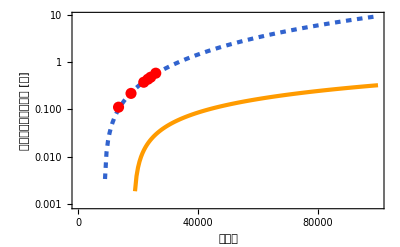

```mathematica
n=100000;
BEM=Table[{x,f[x]/60},{x,0,n,500}];
linear=Table[{x,F[x]/60},{x,0,n,500}];
ListLogPlot[{data,BEM,linear},
PlotTheme->"Web",
PlotStyle->{{Red,PointSize[0.02]},{Dashing[0.01]},Automatic},
Joined->{False,True,True},
PlotRange->{{0,n},All},
Frame->True,
FrameStyle->Directive@{Black,FontFamily->"Time"},
TicksStyle->Black,
FrameLabel->{"節点数","離散化に要する時間 [分]"},
GridLines->Automatic
]
```

```mathematica
2065.143479345168/60
```

34.4191